# Bezruk Yurii, Facultet comp'uterniyh naukh, 2 kurs, variant 1.

## Тема 1. Введення в систему Mathematica.

Завдання 1. Арифметичні обчислення.

Задача 1.1.1  Обчислити значення арифметичного виразу.

```mathematica
(((152+3/4)-(148+3/8)) 0.3)/0.2
```

6.5625

Завдання 2. Обчислення виразу з елементарними функціями.

Задача 1.2.1 Використовуючи систему «Mathematica», обчислити вираз.

```mathematica
y= Sin[√3]+Sin[3 √2]^2/(3 Cos[6 √3]);
```

```mathematica
N[y]
```

0.519876

## Тема 2. Алгебраїчні обчислення

Завдання 1. Алгебраїчні перетворення.

Задача 2.1.1 Використовуючи систему «Mathematica», спростити вираз.

```mathematica
Remove[a,b,c]
```

```mathematica
Simplify[(a^2-b^2-c^2+2 b c)/((a+b-c)/(a+b+c))]
```

(a-b+c) (a+b+c)

Завдання 2. Обчислення значень алгебраїчних виразів.

Задача 2.2.1 Використовуючи систему «Mathematica», обчислити значення виразу при вказаних значеннях параметрів

```mathematica
Remove[a,b]Simplify[b/(a-b) ((a^2-2a b+b^2)(a^2-b^2)(a+b))^(1/3) * (a^3-b^3)/(((a+b)^2)^(1/3))]/.{a->5, b->3}
```

294

Завдання 3. Розв' язання рівнянь.

Задача 2.3.1 Використовуючи систему «Mathematica», розв' язати рівняння

```mathematica
Remove[x, a,b,c]Simplify[Solve[(3a b c)/(a+b)+(a^2 b^2)/(a+b)^3+((2 a+b) b^2 x)/(a(a+b)^2)==3 c x +(b x)/a, x]]
```

{{x->(a b)/(a+b)}}

## Тема 3. Елементи аналітичної геометрії.

Завдання 1. Робота з векторами.

Задача 3.1.1 Використовуючи систему «Mathematica», з' ясувати, чи колінеарні вектори c1 і c2, які побудовані по векторам a та b.Знайти довжину векторів a і b, та кут між ними.В системі Mathematica намалювати вектори a і b.

```mathematica
Remove[a,b,c1,c2]a={1,-2,3}b={3,0,-1}c1 = 2 a+4bc2 = 3b-a
```

{1,-2,3}

{3,0,-1}

{14,-4,2}

{8,2,-6}

```mathematica
c1/c2
```

{7/4,-2,-1/3}

```mathematica
Norm[a]Norm[b]
```

√14

√10

```mathematica
(N[VectorAngle[a,b]]*180)/π
```

90.

```mathematica
z={0,0,0}Graphics3D[{Thickness[0.02],Arrowheads[0.1],Arrow[{z,a}],Arrow[{z,b}]},Axes->True,AxesLabel->{"X","Y","Z"}]
```

{0,0,0}

-Graphics3D-

Завдання 2. Геометричні обчислення в трикутнику.

Задача 3.2.1 Використовуючи систему «Mathematica», знайти довжини сторін, величини кутів та площу трикутника з вершинами в точках A, B, C.

```mathematica
Unprotect[C]A = {1,-2,3};B = {2,-1,2};C = {3,-4, 5};ListPlot3D[{A,B,C},BoxRatios->Automatic]
```

{}

-Graphics3D-

```mathematica
AB=B-AAC=C-ABC=C-B
```

{1,1,-1}

{2,-2,2}

{1,-3,3}

```mathematica
LAB = Norm[AB]LAC = Norm[AC]LBC = Norm[BC]{LAB,LAC,LBC}
```

√3

2 √3

√19

```mathematica
{√3,2 √3,√19}aA=VectorAngle[AB,AC]aB = VectorAngle[-AB,BC]aC = VectorAngle[AC,BC]{aA,aB,aC}
```

{√3,2 √3,√19}

ArcCos[-1/3]

ArcCos[5/(√57)]

ArcCos[7/(√57)]

```mathematica
{ArcCos[-1/3],ArcCos[5/(√57)],ArcCos[7/(√57)]}N[{aA,aB,aC}*180/π]
```

{ArcCos[-1/3],ArcCos[5/(√57)],ArcCos[7/(√57)]}

{109.471,48.5271,22.0017}

```mathematica
S=1/2 Norm[Cross[AB,AC]]
```

2 √2

Завдання 3. Геометричні обчислення в тетраедрі.

Задача 3.3.1 Використовуючи систему «Mathematica», обчислити об' єм тетраедра з вершинами в точках A, B, C, D, та його висоту, яка випущена з вершини D на грань ABC.Графічно зобразити тетраедр і його висоту.

```mathematica
Unprotect[C,D,E];A={-2,-6,-4}B={-1,7,1}C={4,-8,-4}D={1,-4,6}P1=Graphics3D[{Thickness[0.02],Line[{A,B,C,A,D,B,C,D}]},AxesLabel->{"X","Y","Z"},Axes->True]
```

{-2,-6,-4}

{-1,7,1}

{4,-8,-4}

{1,-4,6}

-Graphics3D-

```mathematica
AB=B-A;AC=C-A;AD=D-A;V=1/6 Abs[Det[{AB,AC,AD}]]
```

355/3

```mathematica
n=Cross[AB,AC];S=1/2 Norm[n]
```

5 √74

```mathematica
hh=Solve[1/3 S*h==V,h]
```

{{h->71/(√74)}}

```mathematica
Unprotect[E]h=hh[[1,1,2]]E=D-n/Norm[n]*h;p2=ListPointPlot3D[{E},PlotStyle->{Directive[PointSize[0.06],Red]}];p3=Graphics3D[{Thickness[0.02],Line[{D,E}]}];Show[P1,p2,p3]
```

{}

71/(√74)

-Graphics3D-

## Тема 4. Матричне числення.

Завдання 1. Робота з матрицями.

Задача 4.1.1 Використовуючи систему «Mathematica», знайти значення матричного многочлена 2 A^2+3А+5Е, якщо E одинична матриця.Знайти обернену матрицю A^-1.Обчислити визначник матриці A.Обчислити суму та різницю матриць A і B.Обчислити матричний А.В та поелементний добуток А*В матриць, обчислити різницю між цими добутками.Розв' язати матричне рівняння АХ=В відносно матриці X.

```mathematica
A={{1,0,2},{3,-1,0},{1,1,-2}};M=2*A.A+3*A+5*IdentityMatrix[3];M//MatrixForm
```

(14 | 4 | 2
9 | 4 | 12
7 | -3 | 11)

```mathematica
A1=Inverse[A]
```

{{1/5,1/5,1/5},{3/5,-2/5,3/5},{2/5,-1/10,-1/10}}

```mathematica
MatrixForm[A1]
```

(1/5 | 1/5 | 1/5
3/5 | -2/5 | 3/5
2/5 | -1/10 | -1/10)

```mathematica
Det[A]
```

10

```mathematica
B={{2,1,0},{3,0,4},{1,-1,-2}};A+B//MatrixForm
```

(3 | 1 | 2
6 | -1 | 4
2 | 0 | -4)

```mathematica
A-B//MatrixForm
```

(-1 | -1 | 2
0 | -1 | -4
0 | 2 | 0)

```mathematica
A.B//MatrixForm
```

(4 | -1 | -4
3 | 3 | -4
3 | 3 | 8)

```mathematica
A*B//MatrixForm
```

(2 | 0 | 0
9 | 0 | 0
1 | -1 | 4)

```mathematica
A.B-A*B//MatrixForm
```

(2 | -1 | -4
-6 | 3 | -4
2 | 4 | 4)

```mathematica
X=A1.B
```

{{6/5,0,2/5},{3/5,0,-14/5},{2/5,1/2,-1/5}}

```mathematica
X//MatrixForm
```

(6/5 | 0 | 2/5
3/5 | 0 | -14/5
2/5 | 1/2 | -1/5)

Завдання 2. Робота з матрицями і векторами.

Задача 4.2.1 Дано вектор x та матриці A і B.Використовуючи систему «Mathematica», обчислити вектор y, який заданий в таблиці матричним виразом, а також вектор(АВ-ВА)х Розв' язати рівняння Аu=x за допомогою оберненої матриці та правила Крамера.Для кожного стовпця і рядка матриці А знайти суму елементів. Знайти максимальний і мінімальний елементи матриці В.

```mathematica
x={5,-2,3};A={{1,0,2},{3,-1,0},{1,1,-2}};B= {{2,1,0},{3,0,4},{1,-1,-2}};y = (B-A+B.B).x
```

{40,38,-17}

```mathematica
(A.B-B.A).x
```

{-29,-24,33}

```mathematica
u=Inverse[A].x
```

{6/5,28/5,19/10}

```mathematica
u= LinearSolve[A,x]
```

{6/5,28/5,19/10}

```mathematica
A1 = Join[Transpose[{x}],A[[All,2;;3]],2];A1//MatrixForm
```

(5 | 0 | 2
-2 | -1 | 0
3 | 1 | -2)

```mathematica
A2 = Join[A[[All,1;;1]],Transpose[{x}],A[[All,3;;3]],2];A2//MatrixForm
```

(1 | 5 | 2
3 | -2 | 0
1 | 3 | -2)

```mathematica
A3 = Join[A[[All,1;;2]],Transpose[{x}],2]A3//MatrixForm
```

{{1,0,5},{3,-1,-2},{1,1,3}}

(1 | 0 | 5
3 | -1 | -2
1 | 1 | 3)

```mathematica
{Det[A1],Det[A2],Det[A3]}/Det[A]
```

{6/5,28/5,19/10}

```mathematica
Total[A]
```

{5,0,0}

```mathematica
Total[A,{2}]
```

{3,2,0}

```mathematica
Max[B]
```

4

```mathematica
Min[B]
```

-2

Завдання 3. Створення матриць.

Задача 4.3.1. Згенеруйте одновимірний масив з 16 випадкових дійсних чисел. Відсортуйте його за спаданням і перетворіть на матрицю A розміром 4 x 4. Створіть матрицю B розміром 4 x 4 складену з одних п' ятірок. Згенеруйте матрицю C розміром 4 x 4, елементи якої C_(i,j) обчислюються за формулою C_(i,j)=i^2-j^2. Згенеруйте діагональний масив D з елементами на діагоналі [1,-1,2,-2].Обчисліть масив A+B-C-D+E-3, де E одинична матриця розміром 4 x 4.

```mathematica
M0=RandomReal[16,{16}]M0 =ReverseSort[M0]
```

{12.2199,12.2882,3.95127,9.53597,9.261,1.12891,0.0262111,1.13576,2.02566,6.13159,6.22563,14.8428,5.96336,12.2581,9.74216,0.00575915}

{14.8428,12.2882,12.2581,12.2199,9.74216,9.53597,9.261,6.22563,6.13159,5.96336,3.95127,2.02566,1.13576,1.12891,0.0262111,0.00575915}

```mathematica
A=Table[M0[[i;;i+3]],{i, 1, 13, 4}]A//MatrixForm
```

{{14.8428,12.2882,12.2581,12.2199},{9.74216,9.53597,9.261,6.22563},{6.13159,5.96336,3.95127,2.02566},{1.13576,1.12891,0.0262111,0.00575915}}

(14.8428 | 12.2882 | 12.2581 | 12.2199
9.74216 | 9.53597 | 9.261 | 6.22563
6.13159 | 5.96336 | 3.95127 | 2.02566
1.13576 | 1.12891 | 0.0262111 | 0.00575915)

```mathematica
B = Table[5,4,4]B//MatrixForm
```

{{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5}}

(5 | 5 | 5 | 5
5 | 5 | 5 | 5
5 | 5 | 5 | 5
5 | 5 | 5 | 5)

```mathematica
Unprotect[C]C = Table[i^2-j^2, {i,4},{j,4}]C//MatrixForm
```

{C}

{{0,-3,-8,-15},{3,0,-5,-12},{8,5,0,-7},{15,12,7,0}}

(0 | -3 | -8 | -15
3 | 0 | -5 | -12
8 | 5 | 0 | -7
15 | 12 | 7 | 0)

```mathematica
Unprotect[D]D = DiagonalMatrix[{1,-1,2,-2}]D//MatrixForm
```

{}

{{1,0,0,0},{0,-1,0,0},{0,0,2,0},{0,0,0,-2}}

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | -2)

```mathematica
Unprotect[E]E = IdentityMatrix[4]E//MatrixForm
```

{E}

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
F=A+B -C -D+E -3F//MatrixForm
```

{{16.8428,17.2882,22.2581,29.2199},{8.74216,13.536,16.261,20.2256},{0.131587,2.96336,4.95127,11.0257},{-11.8642,-8.87109,-4.97379,5.00576}}

(16.8428 | 17.2882 | 22.2581 | 29.2199
8.74216 | 13.536 | 16.261 | 20.2256
0.131587 | 2.96336 | 4.95127 | 11.0257
-11.8642 | -8.87109 | -4.97379 | 5.00576)

## Тема 5. Розв'язання рівнянь та систем рівнянь

Завдання 1. Розв' язання рівнянь.

Задача 5.1.1. Використовуючи функцію Solve системи Mathematica, розв' язати
рівняння.

```mathematica
Simplify[Solve[√(3 x -2)==2 √(x+2)-2, x]]
```

{{x->2},{x->34}}

Завдання 2. Розв' язання систем лінійних рівнянь.

Задача 5.2.1. Використовуючи систему «Mathematica», розв' язати систему
  рівнянь п' ятьма способами за допомогою функцій Solve, LinearSolve, RowReduce, за допомогою оберненої матриці та правила Крамера.

```mathematica
Remove[x,y,z]Solve[{2x-4y+3z==9, 3x-5y+z==-4, 4x-7y+z==5}, {x,y,z}]
```

{{x->-47,y->-28,z->-3}}

```mathematica
LinearSolve[{{2,-4,3},{3,-5,1},{4,-7,1}},{9,-4,5}]
```

{-47,-28,-3}

```mathematica
RowReduce[{{2,-4,3,9},{3,-5,1,-4},{4,-7,1,5}}]//MatrixForm
```

(1 | 0 | 0 | -47
0 | 1 | 0 | -28
0 | 0 | 1 | -3)

```mathematica
A={{2,-4,3},{3,-5,1},{4,-7,1}}b={9,-4,5}
```

```mathematica
Inverse[A].b
```

{-47,-28,-3}

```mathematica
{Det[Join[Transpose[{b}],A[[All,2;;3]],2]],Det[Join[A[[All,1;;1]],Transpose[{b}],A[[All,3;;3]],2]],Det[Join[A[[All,1;;2]],Transpose[{b}],2]]}/Det[A]
```

{-47,-28,-3}

Завдання 3. Розв' язання систем нелінійних рівнянь.

Задача 5.3.1. Розв' язати систему нелінійних рівнянь за допомогою функцій
  Solve.Надрукувати лише дійсні розв' язки.

```mathematica
Remove[x,y]Simplify[Solve[{x^2+y^2==2 (x y +2),x+y==6},{x,y},Reals]]
```

{{x->2,y->4},{x->4,y->2}}

## Тема 6. Функції і графіки.

Завдання 1. Побудова графіка функції по точках.

Задача 6.1.1. Використовуючи систему «Mathematica», побудувати графік
функції y(х) та її таблицю значень.Інтервал змінення незалежної змінної
підібрати самостійно.Побудувати графік ламаної, використовуючи таблицю
значень.На одному малюнку одночасно зобразити графік функції та ламаної.

1-(-2 x+x^2)^(1/3)

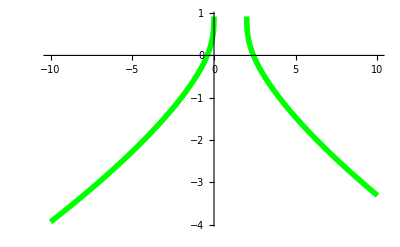

```mathematica
Remove[x,y, p1, p2]y[x_]=1-(x^2-2x)^(1/3)p1= Plot[y[x],{x,-10,10},PlotStyle->{Thickness[0.01],Green}]
```

```mathematica
pt=Table[{x,y[x]},{x,-10,10,1}]
```

{{-10,1-2 15^(1/3)},{-9,1-3^(2/3) 11^(1/3)},{-8,1-2 10^(1/3)},{-7,1-3^(2/3) 7^(1/3)},{-6,1-2 6^(1/3)},{-5,1-35^(1/3)},{-4,1-2 3^(1/3)},{-3,1-15^(1/3)},{-2,-1},{-1,1-3^(1/3)},{0,1},{1,1-(-1)^(1/3)},{2,1},{3,1-3^(1/3)},{4,-1},{5,1-15^(1/3)},{6,1-2 3^(1/3)},{7,1-35^(1/3)},{8,1-2 6^(1/3)},{9,1-3^(2/3) 7^(1/3)},{10,1-2 10^(1/3)}}

```mathematica
N[pt]//TableForm
```

-10. | -3.93242
-9. | -3.62607
-8. | -3.30887
-7. | -2.97906
-6. | -2.63424
-5. | -2.27107
-4. | -1.8845
-3. | -1.46621
-2. | -1.
-1. | -0.44225
0. | 1.
1. | 0.5 -0.866025 I
2. | 1.
3. | -0.44225
4. | -1.
5. | -1.46621
6. | -1.8845
7. | -2.27107
8. | -2.63424
9. | -2.97906
10. | -3.30887

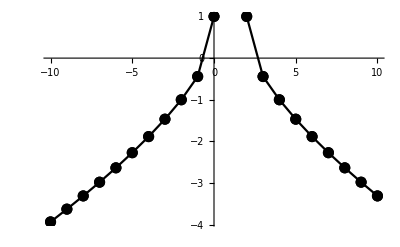

```mathematica
p2=ListPlot[pt,Joined->True,Mesh->Full,PlotStyle->{PointSize[0.02],Black}]
```

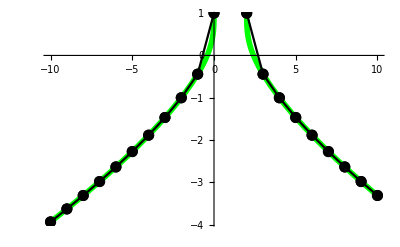

```mathematica
Show[p1,p2]
```

Завдання 2. Побудова графіка полінома.

Задачa 6.2.1. Використовуючи систему «Mathematica», побудувати графік
функції y(x). Інтервал для незалежної змінної підібрати самостійно.

```mathematica
Remove[x,y]
```

```mathematica
y[x_]=2 x^3-9 x^2+12x-9
```

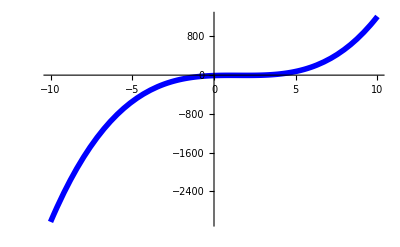

```mathematica
Plot[y[x], {x,-10,10}, PlotStyle->{Thickness[0.01],Blue}]
```

Завдання 3. Побудова графіка явно заданої функції.

Задачa 6.3.1. Використовуючи систему «Mathematica», побудувати графік
функції y(x). Інтервал для незалежної змінної підібрати самостійно.

```mathematica
Remove[x,y]
```

```mathematica
y[x_]=x^2-4x-(x-2)Log[x-1]
```

-4 x+x^2-(-2+x) Log[-1+x]

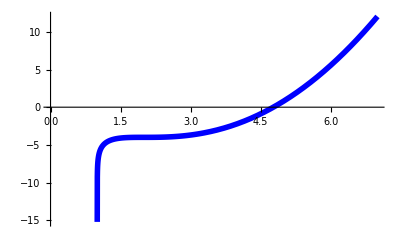

```mathematica
Plot[y[x], {x,0,7}, PlotStyle->{Thickness[0.01],Blue}]
```

Завдання 4. Побудова графіка параметричної функції по точках

Задачa 6.4.1. Використовуючи систему «Mathematica», побудувати графік
функції, яка задана параметрично.Побудувати таблицю координат вузлів
ламаної на інтервалі[ 0, 2π].Побудувати її графік, використовуючи цю
таблицю значень.На одному малюнку одночасно зобразити графік функції та
ламаної.

```mathematica
Remove[x,y,t]
```

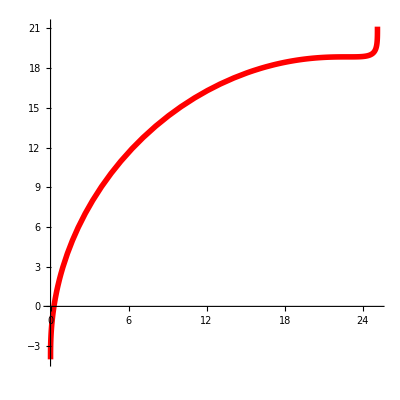

```mathematica
x[t_]=4(t-Sin[t]);y[t_]=4(t-Cos[t]);p1=ParametricPlot[{x[t],y[t]},{t,0, 2π},AspectRatio->Automatic,PlotStyle->{Thickness[0.01],Red}]
```

```mathematica
pt=Table[{x[t],y[t]},{t,0,2π,π/4}]
```

{{0,-4},{4 (-1/(√2)+π/4),4 (-1/(√2)+π/4)},{4 (-1+π/2),2 π},{4 (-1/(√2)+(3 π)/4),4 (1/(√2)+(3 π)/4)},{4 π,4 (1+π)},{4 (1/(√2)+(5 π)/4),4 (1/(√2)+(5 π)/4)},{4 (1+(3 π)/2),6 π},{4 (1/(√2)+(7 π)/4),4 (-1/(√2)+(7 π)/4)},{8 π,4 (-1+2 π)}}

```mathematica
N[pt]//TableForm
```

0. | -4.
0.313166 | 0.313166
2.28319 | 6.28319
6.59635 | 12.2532
12.5664 | 16.5664
18.5364 | 18.5364
22.8496 | 18.8496
24.8196 | 19.1627
25.1327 | 21.1327

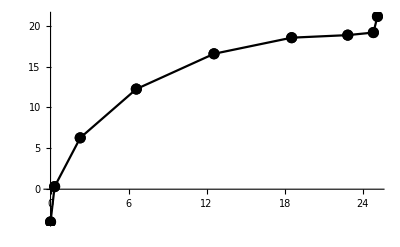

```mathematica
p2=ListPlot[pt,Joined->True,Mesh->Full,PlotStyle->{PointSize[0.02],Black}]
```

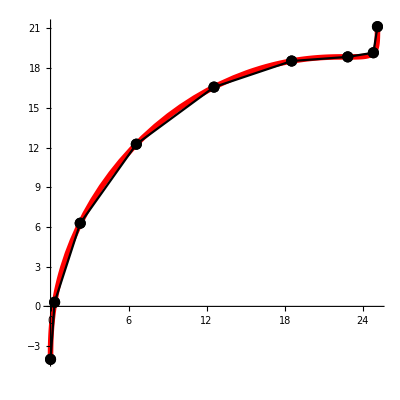

```mathematica
Show[p1,p2]
```

Завдання 5. Побудова графіка функції, яка задана параметрично.

Задачa 6.5.1. Використовуючи систему «Mathematica», побудувати графік
функції, яка задана параметрично.

```mathematica
Remove[x,y,t]
```

```mathematica
x[t_]=4(Cos[t]+t Sin[t])y[t_]=4(Sin[t]-t Cos[t])
```

4 (Cos[t]+t Sin[t])

4 (-t Cos[t]+Sin[t])

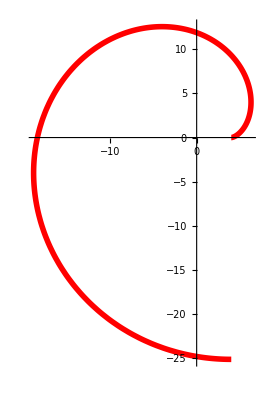

```mathematica
p1=ParametricPlot[{x[t],y[t]},{t,0, 2π},AspectRatio->Automatic,PlotStyle->{Thickness[0.01],Red}]
```

Завдання 6. Побудова графіка функції, яка задана неявно.

Задачa 6.6.1. Використовуючи систему «Mathematica», побудувати графік
функції, яка задана неявно.Діапазони зміни незалежних змінних підібрати
самостійно.

```mathematica
Remove[x,y,F]
```

1+2 x-x^2-4 y+4 x y-y^2

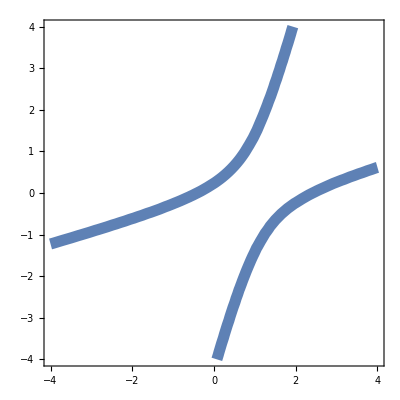

```mathematica
F[x_,y_]=-x^2-y^2+4x y+2x-4y+1ContourPlot[F[x,y]==0,{x,-4,4},{y,-4,4},ContourStyle->{Thickness[0.02]}]
```

## Тема 7. Геометричні побудови.

Завдання 1. Побудова площини по трьом точкам.

Задачa 7.1.1. Скласти рівняння площини, яка проходить через точки A, B та C.Графічно зобразити точки та площину.Діапазон зміни x,y,z підібрати так, щоб точки були розташовані на площині.

```mathematica
Unprotect[C];A={-3,4,-7};B={1,5,-4};C={-5,-2,0};p1=ListPointPlot3D[{A,B,C},PlotStyle->{Directive[PointSize[0.03],Red]}];
```

```mathematica
P={x,y,z};
```

```mathematica
Eq=Det[{P-A,B-A,C-A}];Eq==0
```

57+25 x-34 y-22 z==0

```mathematica
p2=ContourPlot3D[Eq==0,{x,-10,10},{y,-10,10},{z,-10,10},Mesh->None,ContourStyle->Opacity[0.5]];Show[p1,p2,PlotRange->All,AspectRatio->Automatic]
```

-Graphics3D-

Завдання 2. Паралелограм в просторі.

Задачa 7.2.1. В просторі дано плоский паралелограм, координати трьох вершин
A, B, C якого відомі.Знайти координати четвертої вершини D, яка протилежна
вершині A.Обчислити площу паралелограма.В системі Mathematica
побудувати контур паралелограма, та його вершини.

```mathematica
Remove[A,B,C,D]Unprotect[C,D];A={1,-2,3};B={0,-1,2};C={3,4,5};AB=B-A;AC=C-A;D=A+(AB+AC)
```

{2,5,4}

```mathematica
S=Norm[Cross[AB,AC]]
```

8 √2

```mathematica
p1=Graphics3D[{Thickness[0.01],Line[{A,B,D,C,A}]}];p2=ListPointPlot3D[{A,B,D,C},PlotStyle->{Directive[PointSize[0.03],Red]}];Show[p1,p2]
```

-Graphics3D-

Завдання 3. Обчислення в просторовому трикутнику.

Задачa 7.3.1. У трикутника з вершинами в точках A, B, C знайти висоту h=| BD|, яка проведена з вершини B на протилежну сторону.Знайти також
довжину медіани, проведеної із вершини B на протилежну сторону.В системі
Mathematica побудувати контур трикутник, та його медіану.

```mathematica
Unprotect[C,D]Remove[A,B,C]
```

{}

```mathematica
A={2,2,7};B={0,0,6};C={-2,5,7};p1=Graphics3D[{Thickness[0.02],Line[{A,B,C,A}]}]
```

-Graphics3D-

```mathematica
AB=B-A;AC=C-A;S=1/2 Norm[Cross[AB,AC]]
```

(√221)/2

```mathematica
LAC=Norm[AC];Solve[1/2 h*LAC==S,h]
```

{{h->(√221)/5}}

```mathematica
BA=A-B;BC=C-B;BM=(BA+BC)/2
```

{0,7/2,1}

```mathematica
Norm[BM]
```

(√53)/2

```mathematica
M=B+BM
```

{0,7/2,7}

```mathematica
p2=Graphics3D[{Thickness[0.02],Arrowheads[0.1],Arrow[{B,M}]}];Show[p1,p2,Axes->True,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

Завдання 4. Пряма і площина у просторі.

Задачa 7.4.1. Знайти точку перетинання прямої і площини.Використовуючи
систему «Mathematica», намалювати пряму, площину і точку їх перетинання.

```mathematica
Remove[x,y,z,t];x[t_]=-1*t+2;y[t_]=t+2;z[t_]=-4*t-3;rez=Solve[-3x+y-3z+6==0/.{x->x[t],y->y[t],z->z[t]},t]t0=t/.rez[[1]]
```

{{t->-11/16}}

-11/16

```mathematica
{x0,y0,z0}={x[t0],y[t0],z[t0]}
```

{43/16,21/16,-1/4}

```mathematica
pl=ParametricPlot3D[{x[t],y[t],z[t]},{t,-5,5},PlotStyle->Thickness[0.02]];pp=ContourPlot3D[-3x+y-3z+6==0,{x,-5,5},{y,-5,5},{z,-5,5},Mesh->False];pt=ListPointPlot3D[{{x0,y0,z0}},PlotStyle->{Directive[PointSize[0.05],Red]}];Show[pl,pp,pt,PlotRange->All]
```

-Graphics3D-

## Тема 8. Анімація.Робота з документами Mathematica.

Завдання 1. Анімація кривої.

Задача 8.1.1. Побудувати анімацію руху кривої на заданому відрізку часу

```mathematica
Remove[x,t];Animate[Plot[Sin[x]*Sin[t],{x,0,π},PlotRange->1,PlotLabel->t],{t,0,2π}, AnimationRunning->False]
```

Завдання 2. Анімація руху точки вздовж кривої.

Задачіа 8.2.1. Побудувати анімацію руху точки вздовж заданого відрізка
параметричної кривої.

```mathematica
Remove[x,y,t]
```

```mathematica
x[t_]=5(t-Sin[t]);y[t_]=5(1-Cos[t]);p1=ParametricPlot[{x[tau],y[tau]},{tau,0,2π}];Animate[p2=Graphics[{Green,Disk[{x[t],y[t]},0.5]}];Show[p1,p2],{t,0,2π}]
```

Завдання 3. Оформлення документів в Mathematica.

Задачa 8.3.1. Використовуючи систему «Mathematica», створити підсумковий
звіт, який включає результати виконання поточної та всіх попередніх тем, і
оформлений відповідно описаним в додатку А вимогам.

```mathematica
Pidstumkoviy zvit sformovano.
```

## Тема 9. Обчислення границь та похідних

Завдання 1. Послідовність з раціональним загальним членом

Задачa 9.1.1. Використовуючи систему «Mathematica», обчислити границю
послідовності та надрукувати вісім початкових членів.

```mathematica
Remove[x,n];x[n_]=((3-n)^4-(2-n)^4)/((1-n)^4-(1+n)^4);Table[x[n],{n,1,8}]
```

{-15/16,-1/80,1/240,15/544,1/16,175/1776,369/2800,671/4160}

```mathematica
N[Table[x[n],{n,1,8}],3]
```

{-0.938,-0.0125,0.00417,0.0276,0.0625,0.0985,0.132,0.161}

```mathematica
Limit[x[n],n->∞]
```

1/2

Завдання 2. Послідовність з ірраціональним загальним членом.

Задачa 9.2.1. Використовуючи систему «Mathematica», обчислити границю
послідовності, надрукувати 8 початкових членів в десятковому вигляді, побудувати графік перших 50 членів.

```mathematica
Remove[x,n];x[n_]=(n (5 n^2)^(1/3)+(9 n^8+1)^(1/4))/((n+√n)√(7-n+n^2));N[Table[x[n],{n,1,8}],3]
```

{0.659,1.21,1.54,1.72,1.82,1.87,1.91,1.93}

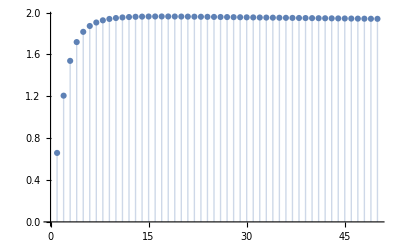

```mathematica
ListPlot[Table[x[n],{n,1,50}],Filling->Axis,PlotRange->All]
```

```mathematica
Limit[x[n],n->∞]
```

√3

Завдання 3. Границі різноманітних функцій.

Задачa 9.3.1. Використовуючи систему «Mathematica», обчислити границю
функції.Перевірити, що значення функції наближаються до границі, коли
аргумент x прямує до граничного значення x0.Для цього побудуйте таблицю
значень функції в околі граничного значення x0

```mathematica
Remove[f,x];f[x_]=(Exp[x]+Exp[-x]-2)/Sin[x]^2;x0=0;y0=Limit[f[x],x->x0]
```

1

```mathematica
f[x0+{0.1,0.01,0.001,0.00001,0.000001}]
```

{1.00418,1.00004,1.,1.,0.999867}

Завдання 4. Границя функції в околі особливої точки.

Задачa 9.4.1. Використовуючи систему «Mathematica», обчислити границю
функції.Перевірити, що гранична точка є особливою точкою функції.Показати, що значення функції наближаються до граничного, коли аргумент x
прямує до граничного значення.Для цього побудувати графік функції і
особливу точку.Діапазон для незалежної змінної підібрати самостійно.

```mathematica
Remove[x,x0,y0,f];f[x_]=((x^3-2x-1)(x+1))/(x^4+4 x^2-5);x0=-1;y0=Limit[f[x],x->x0]
```

0

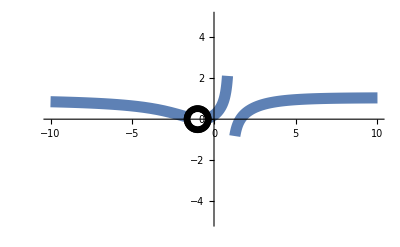

```mathematica
pf=ListPlot[{{x0,y0}},PlotStyle->{Black,PointSize[0.05]}];pw=ListPlot[{{x0,y0}},PlotStyle->{White,PointSize[0.025]}];pline=Plot[f[x],{x,-5,5},PlotStyle->Thickness[0.02]];Show[pline,pf,pw,PlotRange->{{-5,10},{-5,5}},AxesOrigin->{0,0}]
```

Завдання 5. Обчислення похідних

Задача 9.5.1. Використовуючи систему «Mathematica», обчислити похідну y'(х) функції y(x). Побудувати графік функції y(x) та її похідної y'(х).Обчислити значення похідної в точках x= 3, 5.0, 7.

```mathematica
Remove[x,y,y1];y[x_]=(2(3 x^3+4 x^2-x-2))/(15 √(1+x));y1[x_]=Simplify[D[y[x],x]]
```

x √(1+x)

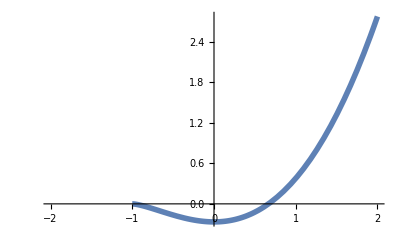

```mathematica
p1=Plot[y[x],{x,-2,2},PlotStyle->Thickness[0.01]]
```

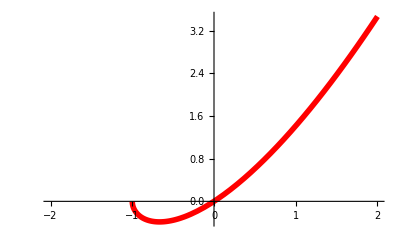

```mathematica
p2=Plot[y1[x],{x,-2,2},PlotStyle->{Thickness[0.01],Red}]
```

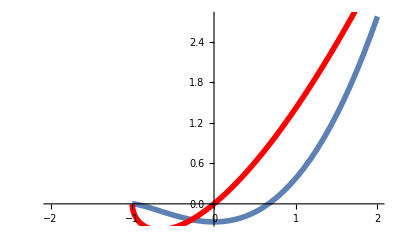

```mathematica
Show[p1,p2]
```

```mathematica
y1[{3,5.0,7}]
```

{6,12.2474,14 √2}

Завдання 6. Похідні виразів, які містять тригонометричні функції.

Задачa 9.6.1. Використовуючи систему «Mathematica», знайти похідну функції y(x)
та побудувати її графік.

```mathematica
Remove[x,y,y1];y[x_]=Sin[√3]+1/3*Sin[3x]^2/Cos[6x];y1[x_]=Simplify[D[y[x],x]]
```

Sec[6 x] Tan[6 x]

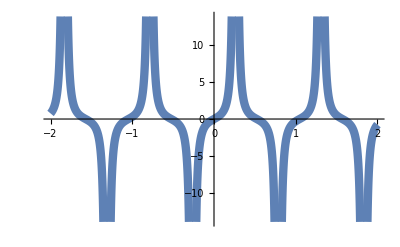

```mathematica
Plot[y1[x],{x,-2,2},PlotStyle->Thickness[0.015]]
```

Завдання 7. Похідні вищих порядків.

Задачa 9.7.1. Використовуючи систему «Mathematica», знайти похідну
зазначеного порядку та побудувати її графік.

```mathematica
Remove[x,y,y5];y[x_]=(2 x^2-7)Log[x-1];y5[x_]=Simplify[D[y[x],{x,5}]]
```

(8 (-11-5 x+x^2))/(-1+x)^5

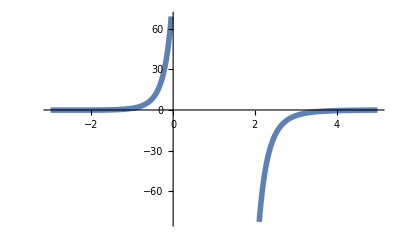

```mathematica
Plot[y5[x],{x,-3,5}, PlotStyle->Thickness[0.01]]
```

Завдання 8. Використання похідних у рівняннях.

Задачa 9.8.1. Використовуючи систему «Mathematica», показати, що функція y(x)
задовольняє рівнянню.В кожному варіанті задана функція та рівняння, якому вона можливо задовольняє.

```mathematica
Remove[x,y,y1];y[x_]=√(x^2-x);y1[x_]=Simplify[D[y[x],x]]
```

(-1+2 x)/(2 √((-1+x) x))

```mathematica
Simplify[2x y[x] y1[x]]==Simplify[x^2+y[x]^2]
```

## Тема 10. Використання диференціального числення.

Завдання 1. Графік дотичної.

Задача 10.1.1. Використовуючи систему «Mathematica», скласти рівняння
дотичної до кривої в точці з абсцисою x0. Побудувати графіки функції і її
дотичної в цій точці.Діапазони зміни x на графіках кривої та дотичної
підбирати самостійно.

```mathematica
Remove[x,y,y1,Y];y[x_]=(4x-x^2)/4;y1[x_]=y'[x]
```

1/4 (4-2 x)

```mathematica
x0=1;Y[x_]=y[x0]+y1[x0](x-x0)
```

3/4+1/2 (-1+x)

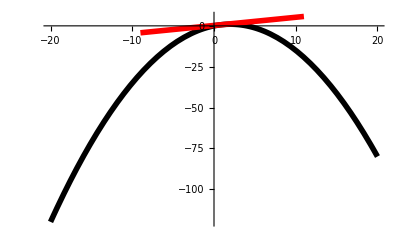

```mathematica
p1=Plot[y[x],{x,-20,20},PlotStyle->{Black,Thickness[0.01]}];p2=Plot[Y[x],{x,x0-10,x0+10},PlotStyle->{Red,Thickness[0.01]}];Show[p1,p2,PlotRange->All]
```

Завдання 2. Дотична та нормаль до параметричної кривої.

Задачa 10.2.1. Використовуючи систему «Mathematica», скласти рівняння
дотичної та нормалі до параметрично заданої кривої в зазначеній точці t0.Побудувати графіки кривої, дотичної і нормалі в цій точці.При побудові
графіків підбирати діапазони зміни параметра t так, щоб крива, точка і прямі
відображали свої характерні ділянки в околі точки дотику.

```mathematica
Remove[x,y,t,t0,p1,p2,p3];
```

```mathematica
x[t_]=Sin[t]^3;y[t_]=Cos[t]^3;t0=π/3;xt[t_]=x[t0]+t*x'[t0]yt[t_]=y[t0]+t*y'[t0]
```

(3 √3)/8+(9 t)/8

1/8-(3 √3 t)/8

```mathematica
xn[t_]=x[t0]+t*y'[t0]yn[t_]=y[t0]-t*x'[t0]
```

(3 √3)/8-(3 √3 t)/8

1/8-(9 t)/8

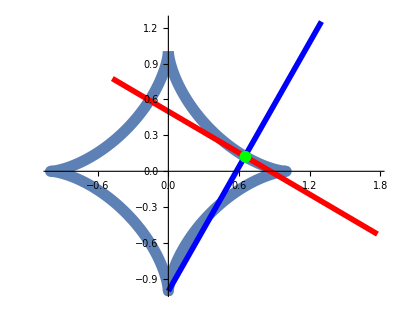

```mathematica
p1=ParametricPlot[{x[t],y[t]},{t,0,2π},PlotStyle->Thickness[0.02],AspectRatio->Automatic];p2=Graphics[{Green,Disk[{x[t0],y[t0]},0.05]}];p3 = ParametricPlot[{xt[t],yt[t]},{t,-1,1},PlotStyle->{Red,Thickness[0.01]}];p4 = ParametricPlot[{xn[t],yn[t]},{t,-1,1},PlotStyle->{Blue,Thickness[0.01]}];Show[p1,p3,p4,p2,PlotRange->All]
```

Завдання 3. Асимптоти.

Задачa 10.3.1. Використовуючи систему «Mathematica», знайти асимптоти
функції y(x). Побудувати графік функції та всі її похилі і горизонтальні
асимптоти.Якщо у функціх є вертикальні асимптоти в точках xi, то ці точки
виключити з графіка.

```mathematica
Remove[x,f,a,b];f[x_]=(17-x^2)/(4x-5);a=Limit[f[x]/x,x->∞]
```

-1/4

```mathematica
b=Limit[f[x]-a x,x->∞]
```

-5/16

```mathematica
a2=Limit[f[x]/x,x->-∞]
```

-1/4

```mathematica
Solve[4x-5==0,x]
```

{{x->5/4}}

```mathematica
Limit[f[x],x->5/4]
```

Indeterminate

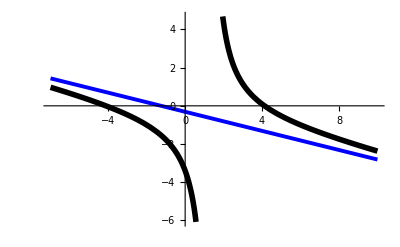

```mathematica
Plot[{f[x],a x+b},{x,-7,10},PlotStyle->{{Black,Thickness[0.01]},{Blue,Thickness[0.007]}}]
```

Завдання 4. Дотична і нормаль до кривої, яка задана неявно.

Задача 10.4.1. Використовуючи систему «Mathematica», скласти рівняння
дотичної та нормалі до кривої, яка задана неявно.Побудувати графіки кривої, її
дотичної та нормалі в точці, яку вибрати самостійно.

```mathematica
Remove[x,y,F,x0,y0,rez]
```

```mathematica
F[x_,y_]=3 x^2+10x y+3 y^2-2x-14y-13
```

-13-2 x+3 x^2-14 y+10 x y+3 y^2

```mathematica
pc1=ContourPlot[F[x,y]==0,{x,-5,5},y{-5,5},ContourStyle->{Black,Thickness[0.01]}] ("Ne znayu, pochemy ne rabotaet, ne puskaet znacheniya Y")
```

ContourPlot::pllim: Range specification {-5 y,5 y} is not of the form {x, xmin, xmax}.

Ne znayu, pochemy ne rabotaet, ne puskaet znacheniya Y ContourPlot[F[x,y]==0,{x,-5,5},y {-5,5},ContourStyle->{Black,Thickness[0.01]}]

```mathematica
x0=2;rez=Solve[F[x0,y]==0,y]
```

{{y->1/3 (-3-2 √6)},{y->1/3 (-3+2 √6)}}

```mathematica
y0=rez[[2]][[1,2]]
```

1/3 (-3+2 √6)

ContourPlot::pllim: Range specification {-5 y,5 y} is not of the form {x, xmin, xmax}.

Show::gcomb: Could not combine the graphics objects in ….

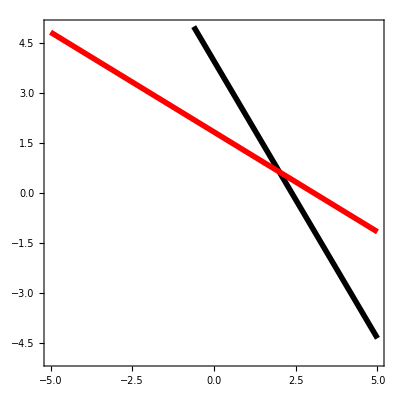
Show[Ne znayu, pochemy ne rabotaet, ne puskaet znacheniya Y ContourPlot[F[x,y]==0,{x,-5,5},y {-5,5},ContourStyle->{Black,Thickness[0.01]}],-Graphics-,AspectRatio->Automatic,GridLines->Automatic]

```mathematica
eqT=Derivative[1,0][F][x0,y0](x-x0)+Derivative[0,1][F][x0,y0](y-y0);eqN=Derivative[1,0][F][x0,y0](y-y0)+Derivative[0,1][F][x0,y0](x-x0);pc2=ContourPlot[{eqT==0,eqN==0},{x,-5,5},{y,-5,5},ContourStyle->{{Black,Thickness[0.01]},{Red,Thickness[0.01]}}];Show[pc1,pc2,AspectRatio->Automatic,GridLines->Automatic]
```

Завдання 5. Найбільше та найменше значення функції на відрізку

Задачa 10.5.1 Використовуючи систему «Mathematica», знайти найбільше та
найменше значення функції y(x) на заданому відрізку.Побудувати графік
функції на відрізку, та позначити на графіку екстремальні точки.

```mathematica
Remove[x,y,p1,p2]
```

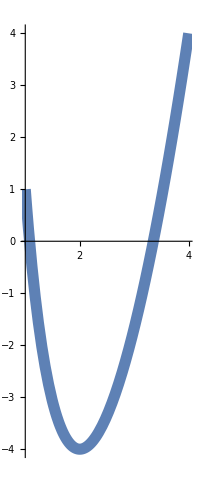

```mathematica
y[x_]=x^2+16/x-16;p1=Plot[y[x],{x,1,4},PlotStyle->Thickness[0.02],AspectRatio->Automatic]
```

```mathematica
min=Minimize[{y[x],1<=x<=4},x]
```

{-4,{x->2}}

```mathematica
ymin=min[[1]];xmin=x/.min[[2]];max=Maximize[{y[x],1<=x<=4},x]
```

{4,{x->4}}

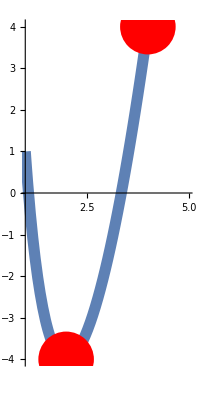

```mathematica
ymax=max[[1]];xmax=x/.max[[2]];p2=ListPlot[{{xmin,ymin},{xmax,ymax}},PlotStyle->{Red,PointSize[0.1]}];Show[p1,p2,PlotRange->{{1,5},{-4,4}}]
```

Завдання 6. Частинні похідні.Нормаль до поверхні

Задачa 10.6.1. Використовуючи систему «Mathematica», обчислити частинні
похідні першого і другого порядків функції.Побудувати графік функції і вектор
нормалі до її поверхні в заданій точці.Щоб нормаль до поверхні виглядала як
нормаль, підібрати пропорції довжин координатних осей графіка, використовуючи опцію BoxRatios.

```mathematica
Remove[x,z,y,x0,y0,p1,p2,P,n];z[x_,y_]=x^2 y-x y^2+1;x0=0.5; y0=-0.5;zx[x_,y_]=D[z[x,y],x]zy[x_,y_]=D[z[x,y],y]
```

2 x y-y^2

x^2-2 x y

```mathematica
Simplify[D[z[x,y],{x,2}]]
```

2 y

```mathematica
Simplify[D[z[x,y],x,y]]
```

2 (x-y)

```mathematica
Simplify[D[z[x,y],{y,2}]]
```

-2 x

```mathematica
P={x0,y0,z[x0,y0]}
```

{0.5,-0.5,0.75}

```mathematica
n={zx[x0,y0],zy[x0,y0],-1}
```

{-0.75,0.75,-1}

```mathematica
p1=Plot3D[z[x,y],{x,-5,5},{y,-5,5},PlotRange->All,Mesh->None];p2=Graphics3D[{Thickness[0.02],Arrowheads[0.1],Arrow[{P,P-n}]}];Show[p1,p2,BoxRatios->{10, 10, 10},AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

```mathematica
Show[p1,p2,BoxRatios->{10, 10, 400},AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

## Тема 11. Невизначений та визначений інтеграл.Кратні інтеграли

Завдання 1. Обчислення невизначеного інтеграла.

Задача 11.1.1. Використовуючи систему «Mathematica», обчислити
невизначений інтеграл.Побудувати графіки підінтегрального виразу та
первісної.

```mathematica
Remove[f,x];f[x_]=(4-3x)Exp[-3x];F[x_]=Integrate[f[x],x]
```

E^(-3 x) (-1+x)

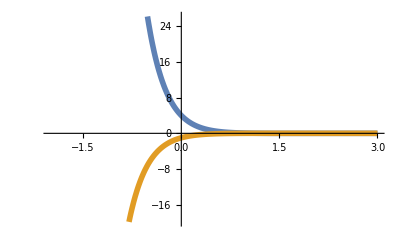

```mathematica
Plot[{f[x],F[x]},{x,-2,3},PlotStyle->Thickness[0.01]]
```

Завдання 2. Невизначений інтеграл різноманітних функцій.

Задачa 11.2.1. Використовуючи систему «Mathematica», обчислити
невизначений інтеграл.Побудувати графік підінтегрального виразу та його
первісної.

```mathematica
Remove[x,f,g,p1,p2]f[x_]=1/(x √(x^2+1));g[x_]=∫f[x]x
```

-ArcTanh[√(1+x^2)]

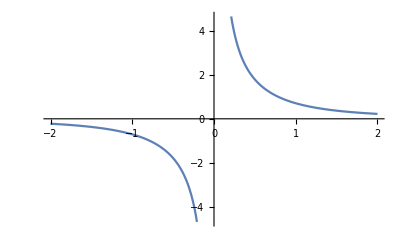

```mathematica
p1=Plot[f[x],{x,-2,2}];p2=Plot[g[x],{x,-1,1}];GraphicsRow[{p1,p2}]
```

Завдання 3. Невизначений інтеграл раціональних функцій.

Задачa 11.3.1. Використовуючи систему «Mathematica», обчислити
невизначений інтеграл.Побудувати графіки підінтегрального виразу, виключивши з нього особливі точки.

```mathematica
Remove[f,q,F]
```

```mathematica
f[x_]=(x^3+6 x^2 13x+9)/((x+1)(x+2)^3);q[x_]=Apart[f[x]]
```

-70/(1+x)+623/(2+x)^3-325/(2+x)^2+149/(2+x)

```mathematica
F[x_]=∫q[x]x
```

-623/(2 (2+x)^2)+325/(2+x)-70 Log[1+x]+149 Log[2+x]

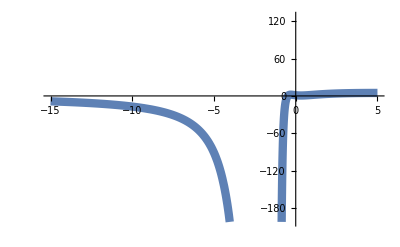

```mathematica
Plot[f[x],{x,-10,5},PlotStyle->Thickness[0.015],Exclusions->{x==-2,x==-1}]
```

Завдання 4. Обчислення визначеного інтеграла.

Задачa 11.4.1. Використовуючи систему «Mathematica», обчислити визначений
інтеграл.Графічно зобразити зону, площу якої він представляє.

```mathematica
Remove[f,x,p1,p2];f[x_]=(x^2+5x+6) Cos[2x];s=Integrate[f[x],{x,-2,0}]
```

1/4 (5-Cos[4]-Sin[4])

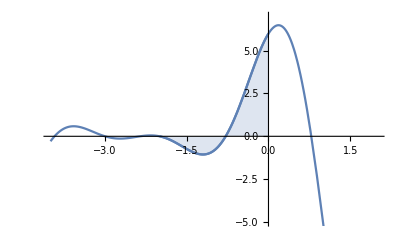

```mathematica
p1=Plot[f[x],{x,-2,0},Filling->Axis];p2=Plot[f[x],{x,-4,2}];Show[p1,p2,PlotRange->{{-4,2},{-5,7}},AxesOrigin->{0,0}]
```

Завдання 5. Визначений інтеграл різноманітних функцій.

Задачa 11.5.1. Використовуючи систему «Mathematica», обчислити визначений
інтеграл.Графічно зобразити зону, площу якої він представляє.

```mathematica
Remove[f,s,p1,p2];f[x_]=(2 Cos[x]+3 Sin[x])/(2Sin[x]-3 Cos[x])^3;s=∫_0^(π/4) f[x]x
```

-17/18

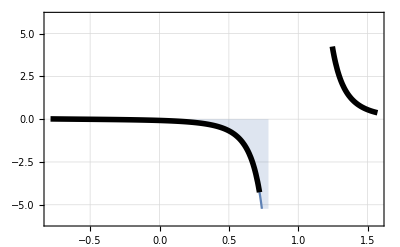

```mathematica
p1=Plot[f[x],{x,0,π/4},Filling->Axis,AxesOrigin->{0,0}];p2=Plot[f[x],{x,-π/4,π/2},PlotStyle->{Thickness[0.01],Black}];Show[{p1,p2},PlotRange->{{-π/4,π/2},{-6,6}},Frame->True,GridLines->Automatic]
```

Завдання 6. Визначений інтеграл від тригонометричних виразів.

Задачa 11.6.1. Використовуючи систему «Mathematica», обчислити визначений
інтеграл.Графічно зобразити зону, площу якої він представляє.

```mathematica
Remove[f,s,p1,p2];f[x_]=2^4 Sin[x]^6 Cos[x]^2;s=∫_0^π f[x]x
```

(5 π)/8

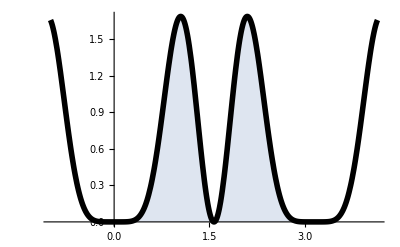

```mathematica
p1=Plot[f[x],{x,0,π},Filling->Axis,AxesOrigin->{0,0}];p2=Plot[f[x],{x,-1,π+1},PlotStyle->{Thickness[0.01],Black}];Show[{p1,p2},PlotRange->All]
```

Завдання 7. Подвійний інтеграл як повторний.

Задачa 11.7.1. Використовуючи систему «Mathematica», обчислити подвійний
інтеграл по області D як повторний.Графічно зобразити область D.

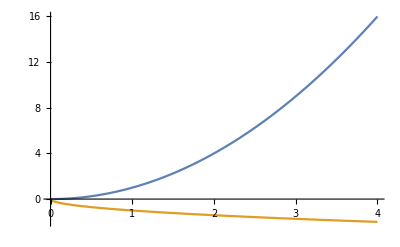

```mathematica
Remove[x,y,y1,y2,p1,p2];y1[x_]=x^2;y2[x_]=-√x;p1=Plot[{y1[x],y2[x]},{x,0,4}]
```

```mathematica
Solve[y1[x]==y2[x],x,Reals]
```

{{x->0}}

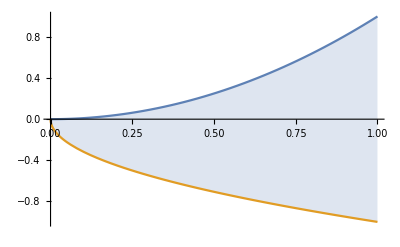

```mathematica
p2=Plot[{y1[x],y2[x]},{x,0,1},Filling->{1->{2}}]
```

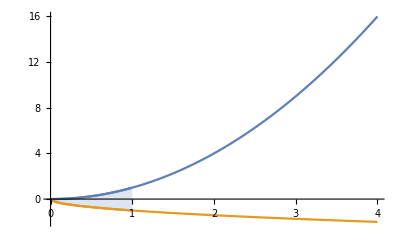

```mathematica
Show[p1,p2]
```

```mathematica
f[x_,y_]=12 x^2 y^2+16 x^3 y^3;Integrate[f[x,y],{x,0,1},{y,-√x,x^2}]
```

1

Завдання 8. Обчислення подвійного інтеграла

Задачa 11.8.1. Використовуючи систему «Mathematica», обчислити подвійний
інтеграл по області D як повторний.Графічно зобразити область D.

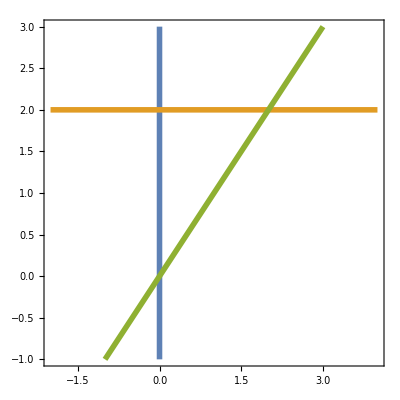

```mathematica
Remove[x,y,p1,p2,f];p1=ContourPlot[{x==0,y-2==0,y-x==0},{x,-2,4},{y,-1,3},ContourStyle->Thickness[0.01]]
```

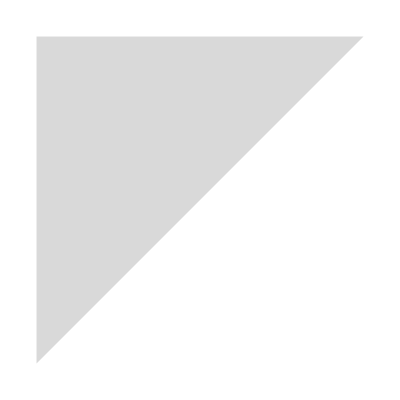

```mathematica
p2=Graphics[{LightGray,Polygon[{{0,0},{0,2},{2,2}}]}]
```

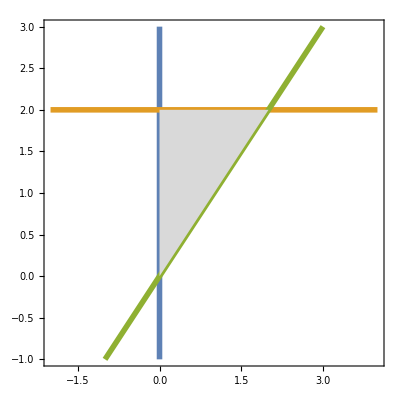

```mathematica
Show[p1,p2,Axes->True]
```

```mathematica
f[x_,y_]=y^2 Exp[-x y/4];F=∫_0^2 ∫_x^2 f[x,y]yx
```

8/E

```mathematica
N[F]
```

2.94304

## Тема 12. Застосування інтегрального числення.

Завдання 1. Обчислення площі між двома кривими, які задані явно.

Задача 12.1.1. Використовуючи систему «Mathematica», обчислити площу
області, яка обмежена графіками функцій.Побудувати графіки функцій та
область, площа якої обчислюється.Якщо в умовах здачі дано інтервал, наприклад, 0 < x < 3
, то точки перетинання шукати не треба, а використати кінцеві точки x1= 0, x2= 3
заданого відрізка.

```mathematica
Remove[y1,y2,x1,x2,x,s,p1,p2];y1[x_]=(x-2)^3;y2[x_]=4x-8;s=Solve[y1[x]==y2[x],x,Reals]
```

{{x->0},{x->2},{x->4}}

```mathematica
x1=x/.s[[1]]x2=x/.s[[2]]x3=x/.s[[3]]
```

0

2

4

```mathematica
p1=Plot[{y1[x],y2[x]},{x,1,6},PlotRange->{{-1,5},{-10,10}}];p2=Plot[{y1[x],y2[x]},{x,x1,x3},Filling->{1->{2}}];
```

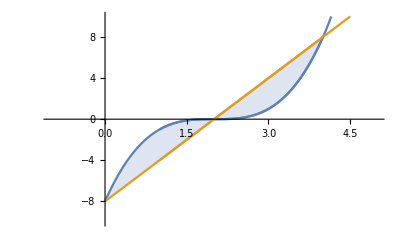

```mathematica
Show[p1,p2]
```

Po svoystvu additivnosti opredelennogo integrala vichiislayem S kak summu dvukh integralov.

```mathematica
Integrate[y2[x]-y1[x],{x,x2,x3}]+Integrate[y1[x]-y2[x],{x,x1,x2}]
```

8

Завдання 2. Обчислення довжини кривої, яка задана явно.

Задачa 12.2.1. Використовуючи систему «Mathematica», обчислити довжину
відрізка кривої, рівняння якої задано в явному вигляді.Побудувати графік
кривої та криволінійного відрізка, довжина якого обчислюється.

```mathematica
y[x_]=2+Cosh[x];x1=0;x2=1;L=∫_x1^x2 √(1+y'[x]^2)x
```

Sinh[1]

```mathematica
N[L]
```

1.1752

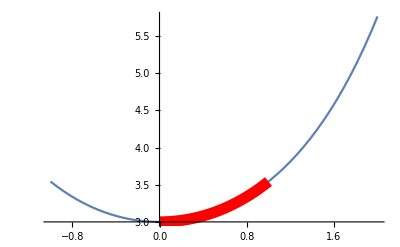

```mathematica
p1=Plot[y[x],{x,-1,2}];p2=Plot[y[x],{x,x1,x2},PlotStyle->{Thickness[0.02],Red}];Show[p1,p2]
```

Завдання 3. Обчислення довжини параметричної кривої

Задачa 12.3.1. Використовуючи систему «Mathematica», обчислити довжину
відрізка кривої, яка задана параметричними рівняннями.Побудувати графік
криволінійного відрізка, довжина якого обчислюється.

```mathematica
Remove[x,y,t];x[t_]=3(2Cos[t]-Cos[2t]);y[t_]=3(2Sin[t]-Sin[2t]);L=Integrate[√(D[x[t],t]^2+D[y[t],t]^2),{t,0,2π}]
```

48

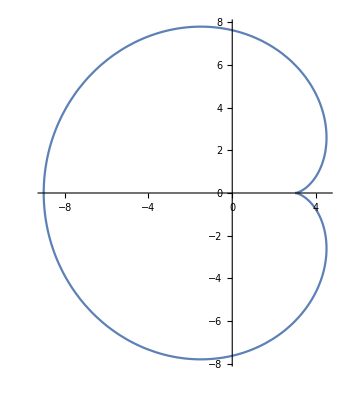

```mathematica
ParametricPlot[{x[t],y[t]},{t,0,2π}]
```

Завдання 4. Обчислення маси платівки.

Задачa 12.4.1. Платівка D задана нерівностями, μ–поверхнева густина.Намалювати платівку та знайти її масу.

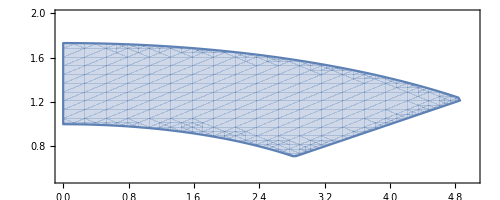

```mathematica
R=(1<= x^2/16+y^2<= 3) && x>=0 && y>=x/4;RegionPlot[R,{x,0,5},{y,0.5,2},AspectRatio->Automatic]
```

```mathematica
mu[x_,y_]=x/y^5;M=Integrate[mu[x,y]*Boole[R],{x,0,4.9},{y,0.8,1.7}]
```

3.61622

Завдання 5. Обчислення об' єму тіла

Задачa 12.5.1. Знайти об' єм тіла, яке задано нерівностями.Побудувати
зображення тіла.

```mathematica
Remove[R,V,x,y,z];
```

```mathematica
R=(1<=x^2+y^2+z^2<=49)&&(-√((x^2+y^2)/35)<=z<= √((x^2+y^2)/3))&&(-x<=y<=0);RegionPlot3D[R,{x,0,7},{y,-7,0.5},{z,-2,4},PlotPoints->50,Boxed->False,AxesOrigin->{0,0,0},Mesh->None]
```

-Graphics3D-

```mathematica
Chop[NIntegrate[Boole[R],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞}]]
```

59.6903

## Тема 13. Інтерполяція і апроксимація.

Завдання 1. Ламана.

Задача 13.1.1. Побудувати рівняння ламаної, яка зображена на рисунку.Координати вузлів взяти з рисунка.Записати рівняння за допомогою формули Бернштейна, за допомогою функцій Piecewise та Interpolation.Для кожного способу побудувати графік.

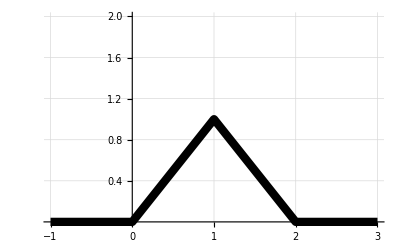

```mathematica
ListPlot[{{-1,0},{0,0},{1,1},{2,0},{3,0}},PlotRange->{{-1,3},{0,2}},PlotStyle->{Thickness[0.015],Black},Joined->True,GridLines->Automatic]
```

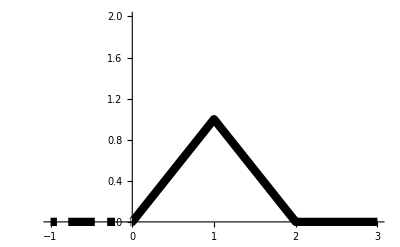

```mathematica
Remove[x,y];y[x_]=1/2 Abs[x]-Abs[x-1] + 1/2 Abs[x-2];Plot[y[x],{x,-1,3},PlotRange->{{-1,3},{0,2}},PlotStyle->{Thickness[0.015],Black}]
```

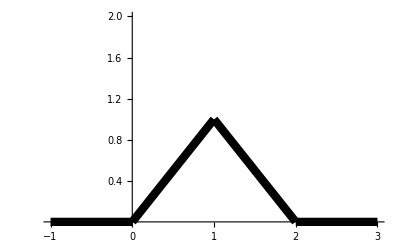

```mathematica
Remove[y];y[x_]=Piecewise[{{0,x<=0},{x,0<x<=1},{2-x,1<x<=2},{0,x>2}}];Plot[y[x],{x,-1,3},PlotRange->{{-1,3},{0,2}},PlotStyle->{Thickness[0.015],Black}]
```

```mathematica
Remove[y]
```

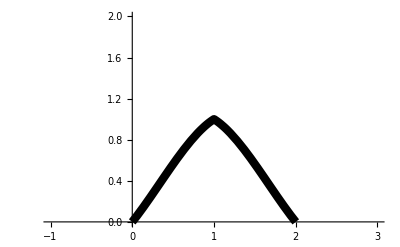

```mathematica
data={{-1,0},{0,0},{1,1},{2,0},{3,0}};y=Interpolation[data];Plot[y[x],{x,-1,3},PlotRange->{{-1,3},{0,2}},PlotStyle->{Thickness[0.015],Black}]
```

Завдання 2. Кускові функції.

Задачa 13.2.1. Використовуючи функцію Piecewise, побудувати графіки
наступних кускових функцій.

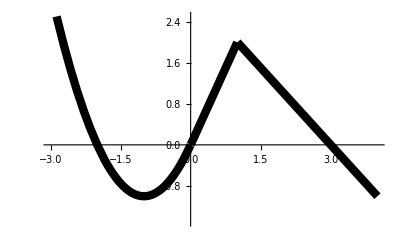

```mathematica
Remove[s,x];s[x_]=Piecewise[{{x(x+2),x<=0},{2x, 0<x<1},{3-x,x>=1}}];Plot[s[x],{x,-3,4},PlotRange->{{-3,4},{-1.5,2.5}},PlotStyle->{Thickness[0.015],Black}]
```

Завдання 3. Поліноміальна інтерполяція множини точок.

Задачa 13.3.1. Дано координати точок на площині.Побудувати інтерполяційний
поліном, який проходить крізь ці точки (знайти рівняння, побудувати графік полінома і зображення точок).

```mathematica
pnts={{1,3},{2,5},{3,3}};P[x_]=Expand[InterpolatingPolynomial[pnts,x]]
```

-3+8 x-2 x^2

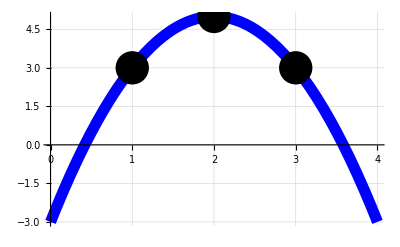

```mathematica
Plot[P[x],{x,0,4},PlotStyle->{Thickness[0.02],Blue},Epilog-> {Black,PointSize[0.06],Point/@pnts},GridLines->Automatic]
```

Завдання 4. Поліноміальна інтерполяція функцій.

Задачі 13.4.На заданому відрізку наблизити задану функцію f (x) за
допомогою інтерполяційного полінома.Побудувати графіки вихідної функції, інтерполяційного полінома і точок, обраних для інтерполяції.

```mathematica
Remove[f,x,P];f[x_]=Sin[x]/(x^2+1);ts=Chop[Table[{x,f[x]},{x,-3,3,1.}]];P[x_]=Chop[Collect[InterpolatingPolynomial[ts,x],x]]
```

0.577016 x-0.167867 x^3+0.0115863 x^5

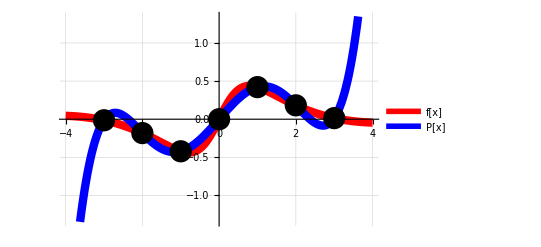

```mathematica
Plot[{f[x],P[x]},{x,-4,4},PlotStyle->{{Thickness[0.015],Red},{Thickness[0.015],Blue}},Epilog->{Black,PointSize[0.04],Point/@ts},GridLines->Automatic,PlotLegends->{"f[x]","P[x]"}]
```

Завдання 5. Поліноміальна інтерполяція параметричних функцій.